## Analysis of SimTree output

```mathematica
demeCount=3;
```

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bedfordt/Documents/current-projects/SimTree/source

```mathematica
SetOptions[Plot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLinePlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLogPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[Graphics,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->False,FrameTicksStyle->Black,ImageSize->600,PlotRange->{0,All}];
```

```mathematica
spatialColors={RGBColor[0.765,0.728,0.274],RGBColor[0.324,0.609,0.708],RGBColor[0.857,0.131,0.132]};
```

```mathematica
spatialColorRules=MapIndexed[#2[[1]]-1->#1&,spatialColors]
```

{0→RGBColor[0.765,0.728,0.274],1→RGBColor[0.324,0.609,0.708],2→RGBColor[0.857,0.131,0.132]}

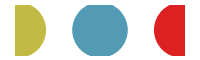

```mathematica
Graphics[{PointSize[0.2],MapIndexed[{#1,Point[{#2[[1]],0}]}&,spatialColors]},AspectRatio->0.3,ImageSize->200]
```

```mathematica
trunkColors={GrayLevel[0.3],Red};
```

```mathematica
trunkColorRules=MapIndexed[#2[[1]]-1->#1&,trunkColors]
```

{0→GrayLevel[0.3],1→RGBColor[1,0,0]}

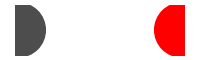

```mathematica
Graphics[{PointSize[0.2],MapIndexed[{#1,Point[{#2[[1]],0}]}&,trunkColors]},AspectRatio->0.3,ImageSize->200]
```

## Assumptions

Let’s say there are 10 sites that function to move the virus in phenotype space

```mathematica
10*0.005*(1/365)
```

0.000136986

Mutations per day

## World-wide SIR

```mathematica
data=Import["out.timeseries","Table"];
```

```mathematica
TableForm[data[[1]],TableHeadings->{Range[30]}]
```

1 | date
2 | diversity
3 | totalN
4 | totalS
5 | totalI
6 | totalR
7 | totalCases
8 | northN
9 | northS
10 | northI
11 | northR
12 | northCases
13 | tropicsN
14 | tropicsS
15 | tropicsI
16 | tropicsR
17 | tropicsCases
18 | southN
19 | southS
20 | southI
21 | southR
22 | southCases

```mathematica
data=Drop[data,1];
```

```mathematica
startTime=data[[1,1]]
```

0.0027

```mathematica
endTime=data[[-1,1]]
```

5.4795

```mathematica
popSize=data[[1,3]]
```

600000

### Prevalence

```mathematica
prev=data[[All,{1,5}]];
```

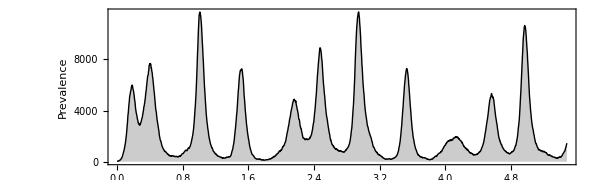

```mathematica
prevfig=ListLinePlot[prev,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->GrayLevel[0.8],FrameLabel->{"","Prevalence"},ImagePadding->{{40,10},{15,5}}]
```

### Incidence

```mathematica
inc=data[[All,{1,7}]];
```

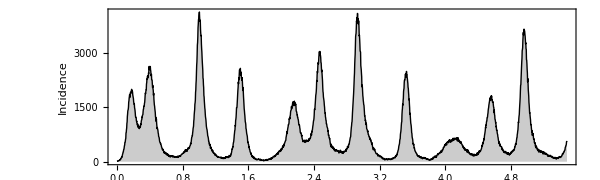

```mathematica
incfig=ListLinePlot[inc,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->GrayLevel[0.8],FrameLabel->{"","Incidence"},ImagePadding->{{40,10},{15,5}}]
```

Mean prevelance

```mathematica
N[Mean[prev[[All,2]]]]
```

2339.37

```mathematica
N[Mean[prev[[All,2]]]/popSize]
```

0.00389894

Mean incidence per year

```mathematica
N[(Total[inc[[All,2]]]/endTime)]
```

284122.

```mathematica
N[(Total[inc[[All,2]]]/endTime)/popSize]
```

0.473537

Flu incidence is 10% per year and prevalence is 0.14%.

### Diversity

```mathematica
div=data[[All,{1,2}]];
```

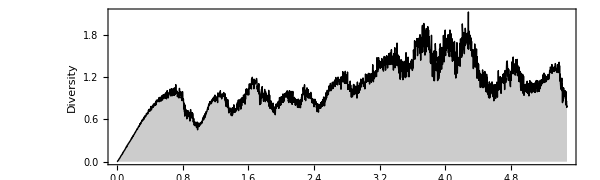

```mathematica
divfig=ListLinePlot[div,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->GrayLevel[0.8],FrameLabel->{"","Diversity"},ImagePadding->{{40,10},{15,5}}]
```

### Combined

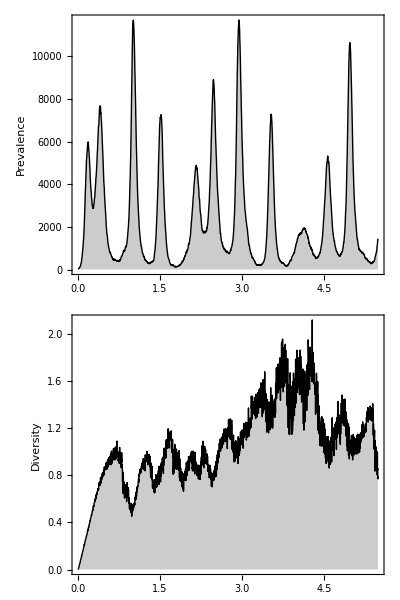

```mathematica
fig=Grid[{{prevfig},{divfig}}]
```

```mathematica
Export["timeseries.pdf",fig,"PDF"]
```

timeseries.pdf

## Regional SIR

```mathematica
data=Import["out.timeseries","Table"];
```

```mathematica
TableForm[data[[1]],TableHeadings->{Range[30]}]
```

1 | date
2 | diversity
3 | totalN
4 | totalS
5 | totalI
6 | totalR
7 | totalCases
8 | northN
9 | northS
10 | northI
11 | northR
12 | northCases
13 | tropicsN
14 | tropicsS
15 | tropicsI
16 | tropicsR
17 | tropicsCases
18 | southN
19 | southS
20 | southI
21 | southR
22 | southCases

```mathematica
data=Drop[data,1];
```

```mathematica
startTime=data[[1,1]]
```

0.0027

```mathematica
endTime=data[[-1,1]]
```

5.4795

### Prevalence

```mathematica
Table[i,{i,10,10+(demeCount-1)*5,5}]
```

{10,15,20}

```mathematica
prevList=Table[data[[All,{1,i}]],{i,10,10+(demeCount-1)*5,5}];
```

```mathematica
max=Max[Map[Max,prevList]]
```

10353

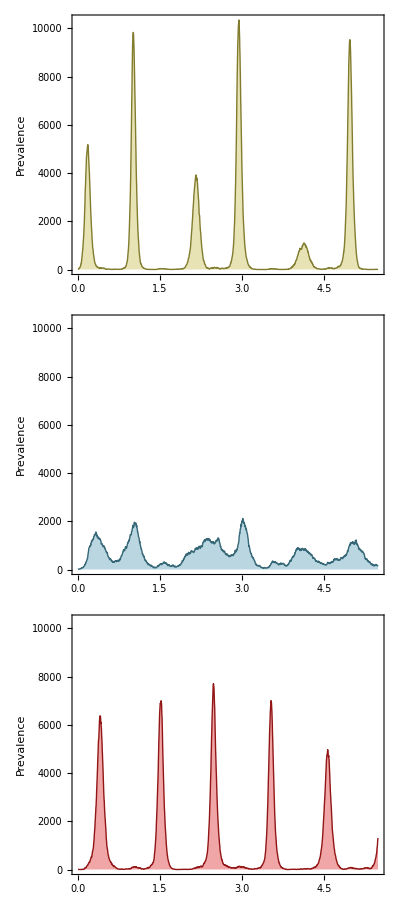

```mathematica
fig=Grid[Table[{ListLinePlot[prevList[[i]],PlotRange->{0,max},AspectRatio->0.15,ImageSize->700,Filling->Axis,PlotStyle->Darker[spatialColors[[i]]],FillingStyle->Directive[Opacity[0.4,spatialColors[[i]]]],FrameLabel->{"","Prevalence"},ImagePadding->{{50,10},{15,5}}]},{i,demeCount}]]
```

```mathematica
Export["timeseriesSpatial.pdf",fig,"PDF"]
```

timeseriesSpatial.pdf

## Tips

```mathematica
tipScale=0.001;
```

```mathematica
tipData=Import["out.tips","CSV"];
```

```mathematica
Length[tipData]
```

11866

```mathematica
traitHeader=tipData[[1]];
```

```mathematica
TableForm[traitHeader,TableHeadings->{Range[7]}]
```

1 | name
2 | year
3 | trunk
4 | location
5 | layout
6 | ag1
7 | ag1

```mathematica
tipData=Drop[tipData,1];
```

```mathematica
name=1;year=2;trunk=3;loc=4;layout=5;ag1=6;ag2=7;
```

### Graphics settings

```mathematica
frameWindow=0.2;
```

```mathematica
plotRange={{Floor[Min[tipData[[All,ag1]]],frameWindow],Ceiling[Max[tipData[[All,ag1]]],frameWindow]},{Floor[Min[tipData[[All,ag2]]],frameWindow],Ceiling[Max[tipData[[All,ag2]]],frameWindow]}}
```

{{-0.2,2.8},{0.,0.}}

```mathematica
aspectRatio=Max[Apply[EuclideanDistance,plotRange[[2]]]/Apply[EuclideanDistance,plotRange[[1]]],0.15]
```

0.15

```mathematica
imageSize=If[aspectRatio>1,600/aspectRatio,600]
```

600

```mathematica
frameTicks=Table[Table[{i,i,{0.01,0}},{i,-10,10,frameWindow}],{2},{2}];
```

### Year vs AG1

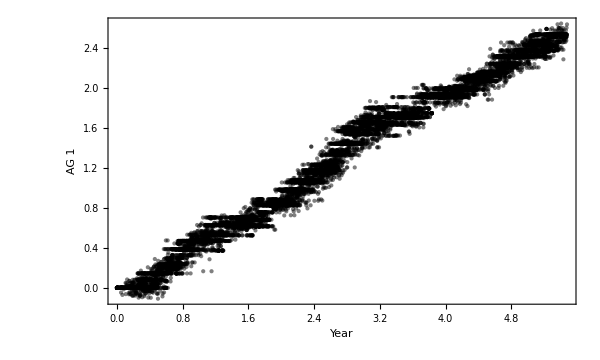

```mathematica
fig=ListPlot[tipData[[All,{year,ag1}]],AspectRatio->0.6,PlotRange->All,PlotStyle->Directive[PointSize[Medium],Black,Opacity[0.5]],FrameLabel->{"Year","AG 1"}]
```

```mathematica
Export["tipsYearAG1.pdf",fig,"PDF"]
```

tipsYearAG1.pdf

### Year vs AG2

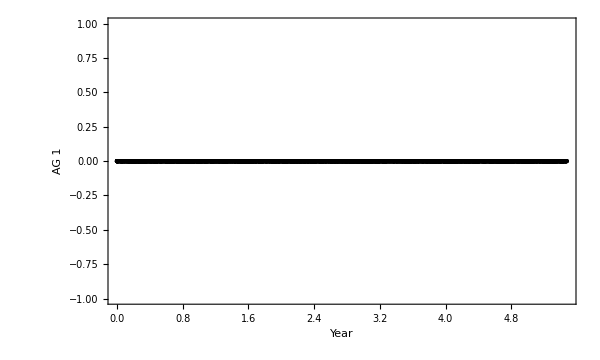

```mathematica
fig=ListPlot[tipData[[All,{year,ag2}]],AspectRatio->0.6,PlotRange->All,PlotStyle->Directive[PointSize[Medium],Black,Opacity[0.5]],FrameLabel->{"Year","AG 1"}]
```

```mathematica
Export["tipsYearAG2.pdf",fig,"PDF"]
```

tipsYearAG2.pdf

### AG1 vs AG2

```mathematica
tallies=Tally[tipData[[All,{ag1,ag2}]]];
```

```mathematica
points=Map[{PointSize[N[tipScale*Sqrt[#[[2]]]]],Point[#[[1]]]}&,tallies];
```

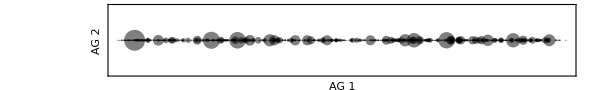

```mathematica
fig=Graphics[{Opacity[0.5],points},AspectRatio->aspectRatio,PlotRange->plotRange,ImageSize->imageSize,FrameLabel->{"AG 1","AG 2"},Frame->{True,True,False,False},FrameTicks->frameTicks]
```

```mathematica
Export["tipsAG1AG2.pdf",fig,"PDF"]
```

tipsAG1AG2.pdf

### Map

```mathematica
jitter=Flatten[Map[Table[#[[1]]+RandomVariate[NormalDistribution[0,0.017],2],{Round[#[[2]]]}]&,tallies],1];
```

```mathematica
Length[jitter]
```

11865

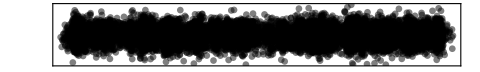

```mathematica
fig=ListPlot[jitter,AspectRatio->aspectRatio,PlotRange->plotRange,PlotStyle->Directive[PointSize[0.01],Black,Opacity[0.5]],GridLines->{Range[-10,10,frameWindow],Range[-10,10,frameWindow]},GridLinesStyle->GrayLevel[0.9],Frame->True,ImageSize->imageSize*0.8,FrameTicks->None]
```

```mathematica
Export["tipsMap.pdf",fig,"PDF"]
```

tipsMap.pdf

### Year vs AG1 - Spatial

```mathematica
points=Table[Select[tipData,#[[loc]]==i&][[All,{year,ag1}]],{i,0,demeCount-1}];
```

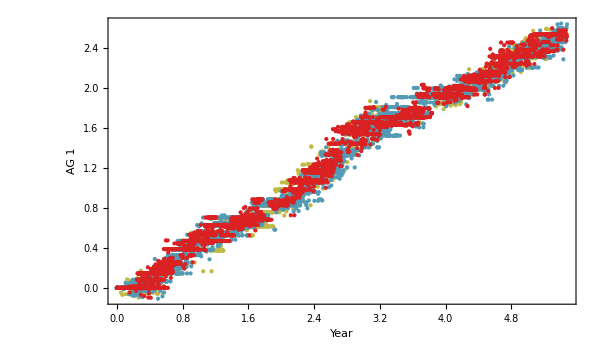

```mathematica
fig=ListPlot[points,AspectRatio->0.6,PlotRange->All,PlotStyle->spatialColors,FrameLabel->{"Year","AG 1"}]
```

```mathematica
Export["tipsYearAG1Spatial.pdf",fig,"PDF"]
```

tipsYearAG1Spatial.pdf

### Spline

```mathematica
data=tipData[[All,{year,ag1}]];
```

```mathematica
fit=Fit[data,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x]
```

0.0798134-1.49843 x+6.01085 x^2-7.51516 x^3+4.75273 x^4-1.65211 x^5+0.320417 x^6-0.0325425 x^7+0.00134951 x^8

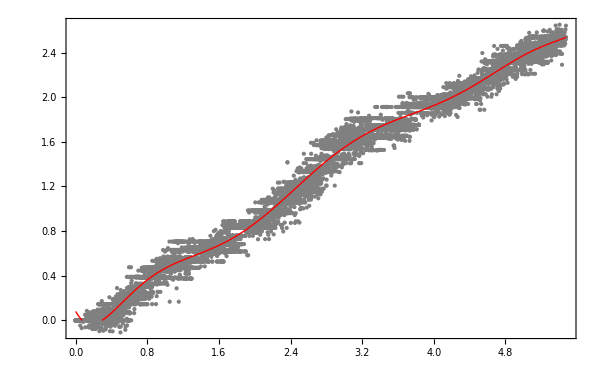

```mathematica
Show[ListPlot[data,PlotStyle->Gray,PlotRange->All],Plot[fit,{x,0,endTime},PlotStyle->Red]]
```

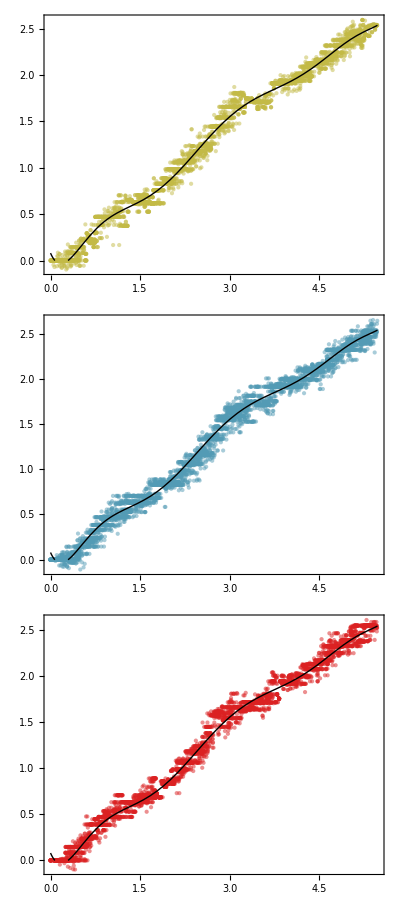

```mathematica
Grid[Table[{Show[ListPlot[Select[tipData,#[[loc]]==i&][[All,{year,ag1}]],PlotStyle->Directive[i/.spatialColorRules,Opacity[0.5]],PlotRange->All,AspectRatio->0.5],Plot[fit,{x,0,endTime},PlotStyle->Directive[Black,Thick]],ImageSize->400]},{i,0,demeCount-1}]]
```

```mathematica
distance[list_]:=Map[((fit/.x->#[[1]])-#[[2]])^2&,list]
```

```mathematica
Mean[distance[data]]
```

0.00585902

```mathematica
standardError[list_]:=StandardDeviation[list]/Sqrt[Length[list]]
```

```mathematica
standardError[distance[data]]
```

0.0000839654

```mathematica
spatialDists=Table[With[{dist=distance[Select[tipData,#[[loc]]==i&][[All,{year,ag1}]]]},{Mean[dist]-standardError[dist],Mean[dist],Mean[dist]+standardError[dist]}],{i,0,demeCount-1}];
```

```mathematica
TableForm[spatialDists,TableHeadings->{Range[3],{"95% lower","mean","95% upper"}}]
```

| 95% lower | mean | 95% upper
1 | 0.00555061 | 0.00569338 | 0.00583615
2 | 0.00593222 | 0.00608471 | 0.0062372
3 | 0.00564745 | 0.00578744 | 0.00592743

```mathematica
chart=MapIndexed[{GrayLevel[0.3],Line[{{#1[[1]],demeCount-#2[[1]]},{#1[[3]],demeCount-#2[[1]]}}],Line[{{#1[[1]],demeCount-#2[[1]]+0.1},{#1[[1]],demeCount-#2[[1]]-0.1}}],Line[{{#1[[3]],demeCount-#2[[1]]+0.1},{#1[[3]],demeCount-#2[[1]]-0.1}}],PointSize[0.03],spatialColors[[#2[[1]]]],Point[{#1[[2]],demeCount-#2[[1]]}]}&,spatialDists];
```

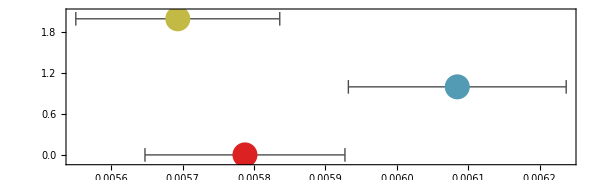

```mathematica
fig=Graphics[chart,AspectRatio->0.3,ImageSize->600,PlotRange->All,Frame->{True,False,True,False},PlotRangePadding->{{0,0},{0.5,0.5}},FrameLabel->{"Distance to AG spline"}]
```

```mathematica
Export["distAGSpatial.pdf",fig,"PDF"]
```

distAGSpatial.pdf

## Trees

```mathematica
branchScale=0.001;tipScale=0.005;clip=0.005;tipScale=0.001;
```

```mathematica
getThickness[count_]:=Thickness[Clip[branchScale*N[Sqrt[count]],{0,clip}]]
```

```mathematica
getPointSize[count_]:=PointSize[N[tipScale*Sqrt[count]]];
```

```mathematica
name=1;year=2;trunk=3;loc=4;layout=5;ag1=6;ag2=7;
```

```mathematica
branchData=ToExpression[Import["out.branches","Table"]];
```

```mathematica
branchData[[1]]
```

{{7875c549,0.,0,1,0.,0.,0.},{42bc0eba,0.,0,1,11.4978,0.,0.},593}

```mathematica
branchData[[1,{1,2},{year,layout}]]
```

{{0.,0.},{0.,11.4978}}

```mathematica
Length[branchData]
```

6500

### Time vs Layout

```mathematica
branchLines=Map[{getThickness[#[[3]]],#[[1,trunk]]/.trunkColorRules,Line[{#[[1,{year,layout}]],{#[[2,year]],#[[1,layout]]},#[[2,{year,layout}]]}]}&,branchData];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

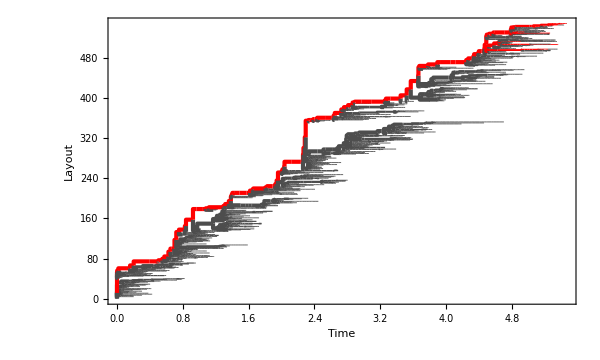

```mathematica
fig=Graphics[branchLines,AspectRatio->0.6,PlotRange->All,ImageSize->600,FrameLabel->{"Time","Layout"},Frame->{True,True,False,False}]
```

### Time vs AG1

```mathematica
branchLines=Map[{getThickness[#[[3]]],#[[1,trunk]]/.trunkColorRules,Line[{#[[1,{year,ag1}]],#[[2,{year,ag1}]]}]}&,branchData];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

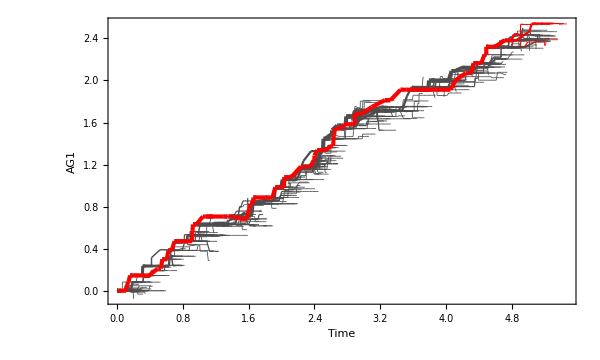

```mathematica
fig=Graphics[branchLines,AspectRatio->0.6,PlotRange->All,ImageSize->600,FrameLabel->{"Time","AG1"},Frame->{True,True,False,False}]
```

### AG1 vs Layout

```mathematica
branchLines=Map[{getThickness[#[[3]]],#[[1,trunk]]/.trunkColorRules,Line[{#[[1,{ag1,layout}]],#[[2,{ag1,layout}]]}]}&,branchData];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

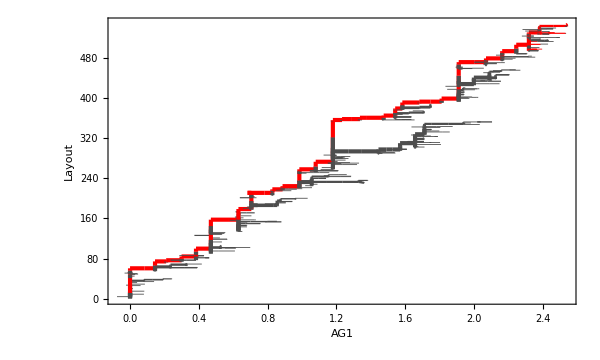

```mathematica
fig=Graphics[branchLines,AspectRatio->0.6,PlotRange->All,ImageSize->600,FrameLabel->{"AG1","Layout"},Frame->{True,True,False,False}]
```

### Time vs Layout with location

```mathematica
branchLines=Map[{getThickness[#[[3]]],#[[1,loc]]/.spatialColorRules,Line[{#[[1,{year,layout}]],{#[[2,year]],#[[1,layout]]},#[[2,{year,layout}]]}]}&,branchData];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

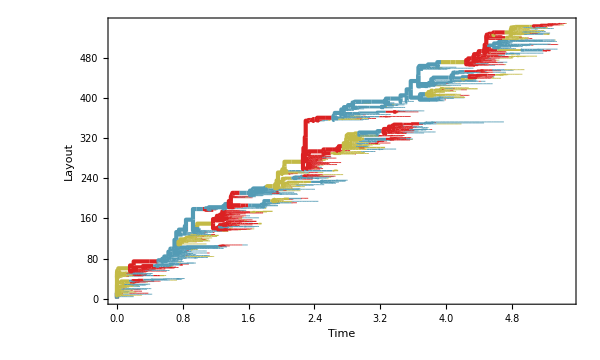

```mathematica
fig=Graphics[branchLines,AspectRatio->0.6,PlotRange->All,ImageSize->600,FrameLabel->{"Time","Layout"},Frame->{True,True,False,False}]
```

### AG1 vs AG2

```mathematica
branchLines=Map[{getThickness[#[[3]]],#[[1,trunk]]/.trunkColorRules,Line[{#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]}]}&,branchData];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

```mathematica
tipPoints=Map[{getPointSize[#[[2]]],Point[#[[1]]]}&,Tally[tipData[[All,{ag1,ag2}]]]];
```

```mathematica
tipPoints={Opacity[0.5],tipPoints};
```

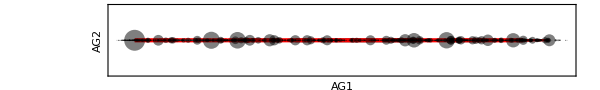

```mathematica
fig=Graphics[{branchLines,tipPoints},AspectRatio->aspectRatio,PlotRange->plotRange,ImageSize->imageSize,FrameLabel->{"AG1","AG2"},Frame->{True,True,False,False},FrameTicks->frameTicks]
```

### AG1 vs AG2 with location

```mathematica
branchLines=Map[{getThickness[#[[3]]],#[[1,loc]]/.spatialColorRules,Line[{#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]}]}&,branchData];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

```mathematica
tipPoints=Map[{getPointSize[#[[2]]],#[[1,3]]/.spatialColorRules,Point[#[[1,{1,2}]]]}&,Tally[tipData[[All,{ag1,ag2,loc}]]]];
```

```mathematica
tipPoints={Opacity[0.5],tipPoints};
```

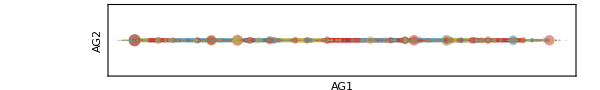

```mathematica
fig=Graphics[{branchLines,tipPoints},AspectRatio->aspectRatio,PlotRange->plotRange,ImageSize->imageSize,FrameLabel->{"AG1","AG2"},Frame->{True,True,False,False},FrameTicks->frameTicks]
```